```mathematica
f[x_]:=√2 x Exp[-(2 x^2-1)/2]
Γf[x_]:=Piecewise[{{-1,x==0},{0,x≠0}}]
```

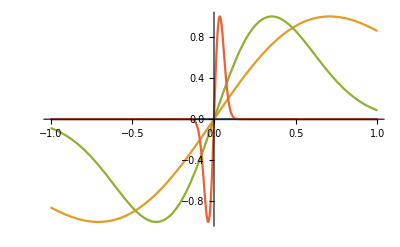

```mathematica
Plot[{Γf[x],f[1x],f[2x],f[20x]},{x,-1,1},PlotRange->All]
```

We are getting for all x > 0 Γ - f (x) <= 0 0 <= Γ - f (x) = > for x > 0 Γ - f (x) = 0

For the x=0, Γ-f(0)<=-1

```mathematica
Γf[0.5]
```

0

(i) For any x, and for x_j→ x lim inf  fj(xj) >= Γ-f(x)
(ii) For any give x , we should be able to find a sequence connverging to x, i.e., x_j→x such that   lim sup f_j(x_j)<=  Γ-f(x)

We are getting for all x>0 Γ-f(x)<= 0 0<=Γ-f(x)=> for x>0 Γ-f(x)=0